# Constructing Term Structure -- Nelson-Siegel

## Equal Weighted

```mathematica
α = 1;
```

```mathematica
R[t_, β0_, β1_, β2_] := β0 + β1 *(1-ⅇ^(-α*t))/(α * t) + β2*(1 - (1 + α * t)*ⅇ^(-α * t))/(α * t);
```

```mathematica
B[t_, β0_, β1_, β2_] := ⅇ^(-t*R[t,β0,β1,β2]);
```

```mathematica
Cp[t_, c_, β0_, β1_, β2_] := 0.5 * ∑_(i=1)^(2*t) c * ⅇ^(i/2 R[i/2,β0,β1,β2])+ ⅇ^(-t*R[t,β0,β1,β2]);
```

```mathematica
{b0, b1, b2} =  {β0,β1,β2}/.Minimize[
(1 - Cp[1, 0.78/ 100, β0, β1, β2])^2 +
(1 - Cp[2, 0.91 / 100, β0, β1, β2])^2+
(1 - Cp[5, 1.26 / 100, β0, β1, β2])^2 +(1 - Cp[10, 1.70/ 100, β0, β1, β2])^2 ,{β0, β1, β2}][[2]]
```

{0.0274762,0.00492522,-0.075346}

## Duration weighted

```mathematica
Dur[t_, c_, β0_, β1_, β2_] := ∑_(i=1)^(2*t) (0.5*c *(i/2) *ⅇ^(-(i/2)*R[i/2,β0,β1,β2]))/Cp[t,c,β0,β1,β2]+ (1*t*ⅇ^(-t*R[t,β0,β1,β2]))/Cp[t,c,β0,β1,β2];
```

```mathematica
{B0, B1, B2} =  {β0,β1,β2}/.Minimize[
(1/Dur[1,0.54∕100,β0,β1,β2])*(1 - Cp[1, 0.54/ 100, β0, β1, β2])^2 +
(1∕Dur[2,0.85∕100,β0,β1,β2])*(1 - Cp[2, 0.85 / 100, β0, β1, β2])^2+
(1∕Dur[5, 1.59∕100,β0,β1,β2])*(1 - Cp[5, 1.59 / 100, β0, β1, β2])^2 +(1∕Dur[10, 2.22∕100,β0,β1,β2])*(1 - Cp[10, 2.22/ 100, β0, β1, β2])^2 ,{β0, β1, β2}][[2]]
```

{0.0383766,-0.0122485,-0.0896862}

## Plot

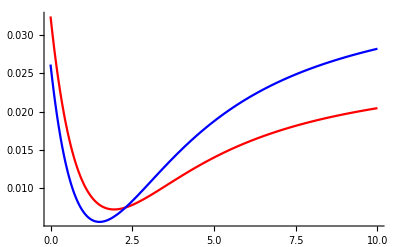

```mathematica
Plot[{R[t,b0,b1,b2],R[t,B0,B1,B2]},{t,0,10},PlotStyle->{Red,Blue}]
```

```mathematica
Cp[5, 5 / 100, b0, b1, b2]
```

1.19014

```mathematica
y= Solve[5*(ⅇ^(-0.5y)+ⅇ^-y+ⅇ^(-1.5y)+ⅇ^(-2y)+ⅇ^(-2.5y)+ⅇ^(-3y)+ⅇ^(-3.5y)+ⅇ^(-4y)+ⅇ^(-4.5y)+ⅇ^(-5y))+100*ⅇ^(-5y)==118.012,y,Reals]
y/.y[[1]]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {y→0.057161}.

Hold[y=Solve[5 (ⅇ^(-0.5 y)+ⅇ^-y+ⅇ^(-1.5 y)+ⅇ^(-2 y)+ⅇ^(-2.5 y)+ⅇ^(-3 y)+ⅇ^(-3.5 y)+ⅇ^(-4 y)+ⅇ^(-4.5 y)+ⅇ^(-5 y))+100 ⅇ^(-5 y)==118.012,y,Reals]]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {y→0.057161}.

Hold[y/.y⟦1⟧]

```mathematica
rr/.Solve[∑_(i=11)^20 0.5*0.05*ⅇ^(-r(0.5*i-5))+1*ⅇ^(-r*5)==1,r,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.0493852}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{{0.0493852→0.0493852}}}

```mathematica
Array[k,10]
```

{0.97561,0.951814,0.928599,0.905951,0.883854,0.862297,0.841265,0.820747,0.800728,0.781198}

```mathematica
Do[k[i-10]=ⅇ^(-rr(i/2-5)),{i,11,20,1}]
```

```mathematica
Array[v,10]
```

{0.0393159,0.0250689,0.0159847,0.0101923,0.00649888,0.00414387,0.00264225,0.00168477,0.00107426,0.000684977}

```mathematica
κ=0.9
σ=0.1
```

0.9

0.1

```mathematica
Do[v[i-10]=1/(2*κ)*σ/κ*ⅇ^(-κ(i/2-5))*(1-ⅇ^(-2κ-5)),{i,11,20,1}]
```

```mathematica
Array[d1,10]
Array[d2,10]
```

{0.324522,0.955004,2.19973,4.54635,8.84075,16.5359,30.1082,53.7508,94.5258,164.269}

{0.285206,0.929936,2.18374,4.53616,8.83425,16.5318,30.1055,53.7492,94.5247,164.269}

```mathematica
Do[d1[i-10]=1/v[i-10]*Log[B[i/2,b0,b1,b2]/(k[i-10]*B[5,b0,b1,b2])]+v[i-10]/2,{i,11,20,1}]
```

```mathematica
Do[d2[i-10]=1/v[i-10]*Log[B[i/2,b0,b1,b2]/(k[i-10]*B[5,b0,b1,b2])]-v[i-10]/2,{i,11,20,1}]
```

```mathematica
t=5
```

5

```mathematica
Poption=∑_(i=1)^(2t) Boole[5<i/2]*0.5*0.05*(B[i/2,b0,b1,b2]*CDF[NormalDistribution[0,1],d1[i-10]]-k[i-10]*B[5,b0,b1,b2]*CDF[NormalDistribution[0,1],d2[i-10]])+(B[10,b0,b1,b2]*CDF[NormalDistribution[0,1],d1[10]]-k[10]*B[5,b0,b1,b2]*CDF[NormalDistribution[0,1],d2[10]])
```

0.0867493

```mathematica
Pcall= Cp[5, 5 / 100, b0, b1, b2]-Poption
```

1.10339